```mathematica
d = 3x+5
```

5+3 x

```mathematica
f=6x-3
```

-3+6 x

```mathematica
d-f
```

8-3 x

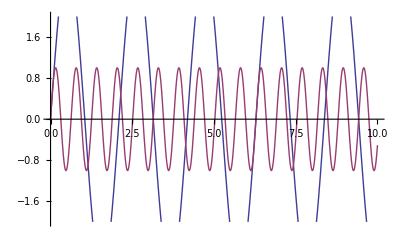

```mathematica
A = 3; f=3;ϕ=0;
a0 =1; f0=10;ϕ0=0;
Plot[{A Sin[f t+ϕ],a0 Sin[f0 t+ϕ0]},{t,0,10},
PlotRange->2]
```

```mathematica
Manipulate[
(*a0=1; f0=10,ϕ0=0;*)
(*A=3;f=3;ϕ=0*)
Plot[{A Sin[f t+ ϕ],a0 Sin[f0 t + ϕ0]},{t,0,10},
PlotRange->2],
{{A,a0,"amplitude"},0,3,Appearance->"Labeled"}
,{{f,f0,"frequency"},0,10,Appearance->"Labeled"}
,{{ϕ,ϕ0,"intrinsic phase"},0,2Pi,Appearance->"Labeled"}]
```